# Physics 230 -- Lab 9 (Data Processing)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 R. Steven Turley, BYU Physics & Astronomy, Fall 2011

Most scientists spend a great deal of time working with data.  In this lab, we will introduce some important tools for importing and exporting a variety of data types to and from Mathematica, and will also practice the art of manipulating complicated multidimensional lists (i.e. arrays) of data.

## File systems (20 min)

### (#1) System Variables (5 min)

(a) Evaluate the cell below to see the Names of all Mathematica functions and symbols that start with the letter "W".

```mathematica
Names["W*"]
```

{WaitAll,WaitNext,WaitUntil,WakebyDistribution,WalleniusHypergeometricDistribution,WaringYuleDistribution,WatershedComponents,WatsonUSquareTest,WattsStrogatzGraphDistribution,WaveletBestBasis,WaveletFilterCoefficients,WaveletImagePlot,WaveletListPlot,WaveletMapIndexed,WaveletMatrixPlot,WaveletPhi,WaveletPsi,WaveletScale,WaveletScalogram,WaveletThreshold,WeatherData,WeberE,Wedge,WeibullDistribution,WeierstrassHalfPeriods,WeierstrassInvariants,WeierstrassP,WeierstrassPPrime,WeierstrassSigma,WeierstrassZeta,WeightedAdjacencyGraph,WeightedAdjacencyMatrix,WeightedGraphQ,Weights,WheelGraph,Which,While,White,Whitespace,WhitespaceCharacter,WhittakerM,WhittakerW,WienerFilter,WignerD,WignerSemicircleDistribution,WindowClickSelect,WindowElements,WindowFloating,WindowFrame,WindowFrameElements,WindowMargins,WindowMovable,WindowOpacity,WindowSelected,WindowSize,WindowStatusArea,WindowTitle,WindowToolbars,WindowWidth,With,WolframAlpha,WolframAlphaDate,WolframAlphaQuantity,WolframAlphaResult,Word,WordBoundary,WordCharacter,WordData,WordSearch,WordSeparators,WorkingPrecision,Write,WriteString,Wronskian}

(b) Beginning with a freshly-started kernel, evaluate the cell below to create a list containing all of the functions and symbols defined within Mathematica, and to count their number.  Most of them are loaded when you start Mathematica, though the list grows when you start defining your own.

```mathematica
Names["*"];
startupnames = %;
Length[startupnames]
```

4177

(c) Many more functions and symbols are added whenever you load additional packages.  Evaluate the cell below to see the new functions and symbols defined after loading the VectorAnalysis package.  Explain to your TA how Complement was used to obtain this list.

```mathematica
<<VectorAnalysis`
currentnames = Names["*"];
Length[currentnames]

newnames = Complement[currentnames,startupnames]
Length[newnames]
```

4225

{ArcLengthFactor,Biharmonic,Bipolar,Bispherical,Cartesian,ConfocalEllipsoidal,ConfocalParaboloidal,Conical,CoordinateRanges,Coordinates,CoordinatesFromCartesian,CoordinatesToCartesian,CoordinateSystem,CrossProduct,currentnames,Cylindrical,Div,DotProduct,Eeta,EllipticCylindrical,Grad,JacobianDeterminant,JacobianMatrix,Laplacian,Llambda,Mmu,Nnu,OblateSpheroidal,ParabolicCylindrical,Paraboloidal,ParameterRanges,Parameters,Pphi,ProlateSpheroidal,Rr,ScalarTripleProduct,ScaleFactors,SetCoordinates,Spherical,startupnames,Toroidal,Ttheta,Uu,Vv,Xx,Xxi,Yy,Zz}

48

(d) Names beginning with the "$" character are called system variables.  Mathematica relies on their values to perform important tasks that are normally transparent to the user.  Sometimes, however, it is useful to monitor or modify the values of system values.  Evaluate the cell below to see their current values, and study the output to find out which $Packages have been installed.

```mathematica
MatrixForm/@{#,ToExpression[#]}&/@Names["$*"]//TableForm
```

$Aborted | $Aborted
$ActivationGroupID | L3346-9762
$ActivationKey | 3346-9762-E7JP8T
$ActivationUserRegistered | True
$AddOnsDirectory | /Library/Mathematica
$AllowDataUpdates | True
$AllowDocumentationUpdates | True
$AllowInternet | True
$AssertFunction | $AssertFunction
$Assumptions | True
$BaseDirectory | /Library/Mathematica
$BatchInput | True
$BatchOutput | False
$BoxForms | (StandardForm
TraditionalForm)
$ByteOrdering | -1
$Canceled | $Canceled
$CharacterEncoding | UTF-8
$CharacterEncodings | (AdobeStandard
ASCII
CP936
CP949
CP950
Custom
EUC-JP
EUC
IBM-850
ISO10646-1
ISO8859-10
ISO8859-11
ISO8859-13
ISO8859-14
ISO8859-15
ISO8859-16
ISO8859-1
ISO8859-2
ISO8859-3
ISO8859-4
ISO8859-5
ISO8859-6
ISO8859-7
ISO8859-8
ISO8859-9
ISOLatin1
ISOLatin2
ISOLatin3
ISOLatin4
ISOLatinCyrillic
Klingon
koi8-r
MacintoshArabic
MacintoshChineseSimplified
MacintoshChineseTraditional
MacintoshCroatian
MacintoshCyrillic
MacintoshGreek
MacintoshHebrew
MacintoshIcelandic
MacintoshKorean
MacintoshNonCyrillicSlavic
MacintoshRomanian
MacintoshRoman
MacintoshRomanPDFExport
MacintoshThai
MacintoshTurkish
MacintoshUkrainian
Math1
Math2
Math3
Math4
Math5
Mathematica1
Mathematica2
Mathematica3
Mathematica4
Mathematica5
Mathematica6
Mathematica7
PrintableASCII
ShiftJIS
Symbol
Unicode
UTF8
WindowsANSI
WindowsBaltic
WindowsCyrillic
WindowsEastEurope
WindowsGreek
WindowsThai
WindowsTurkish
ZapfDingbats)
$CommandLine | (/Applications/Mathematica Home Edition.app/Contents/MacOS/MathKernel
-mathlink
-linkmode
connect
-linkprotocol
SharedMemory
-linkname
4jn_shm)
$CompilationTarget | MVM
$ConditionHold | $ConditionHold
$ConfiguredKernels | («TraditionalForm`2 local kernels»)
$Context | Global`
$ContextPath | (Parallel`Debug`
VectorAnalysis`
PacletManager`
WebServices`
System`
Global`)
$ControlActiveSetting | False
$CreationDate | (2011
2
23
20
18
1)
$CurrentLink | $CurrentLink
$DateStringFormat | (DateTimeShort)
$DefaultFont | (Courier
10.)
$DefaultFrontEnd | $DefaultFrontEnd
$DefaultImagingDevice | Built-in iSight
$DefaultPath | (.
~
/Applications/Mathematica Home Edition.app/Contents/MacOS/Packages
/Applications/Mathematica Home Edition.app/Contents/MacOS/SystemFiles/KernelInit
/Applications/Mathematica Home Edition.app/Contents/MacOS/SystemFiles/GraphicsInit)
$Display | (stdout)
$DisplayFunction | Identity
$DistributedContexts | Global`
$DynamicEvaluation | False
$Echo | {}
$Epilog | Null
$ExportFormats | (3DS
ACO
AIFF
AU
AVI
Base64
Binary
Bit
BMP
Byte
BYU
BZIP2
C
CDF
Character16
Character8
Complex128
Complex256
Complex64
CSV
DICOM
DIF
DIMACS
DOT
DXF
EMF
EPS
ExpressionML
FASTA
FITS
FLAC
FLV
GIF
Graph6
Graphlet
GraphML
GXL
GZIP
HarwellBoeing
HDF
HDF5
HTML
Integer128
Integer16
Integer24
Integer32
Integer64
Integer8
JPEG
JPEG2000
JSON
JVX
KML
LEDA
List
LWO
MAT
MathML
Maya
MGF
MIDI
MOL
MOL2
MTX
MX
NASACDF
NB
NetCDF
NEXUS
NOFF
OBJ
OFF
Package
Pajek
PBM
PCX
PDB
PDF
PGM
PICT
PLY
PNG
PNM
POV
PPM
PXR
QuickTime
RawBitmap
Real128
Real32
Real64
RIB
RTF
SCT
SDF
SND
Sparse6
STL
String
SurferGrid
SVG
SWF
Table
TAR
TerminatedString
TeX
Text
TGA
TGF
TIFF
TSV
UnsignedInteger128
UnsignedInteger16
UnsignedInteger24
UnsignedInteger32
UnsignedInteger64
UnsignedInteger8
UUE
VideoFrames
VRML
VTK
WAV
Wave64
WDX
X3D
XBM
XHTML
XHTMLMathML
XLS
XLSX
XML
XYZ
ZIP
ZPR)
$Failed | $Failed
$FinancialDataSource | YahooFinance
$FormatType | TraditionalForm
$FrontEnd | ⁃ FrontEndObject ⁃
$FrontEndSession | $FrontEndSession
$GeoLocation | (40.39
-111.78)
$HistoryLength | ∞
$HomeDirectory | /Users/spencerlyon2
$IgnoreEOF | False
$ImagingDevices | (Built-in iSight)
$ImportFormats | (3DS
ACO
Affymetrix
AIFF
ApacheLog
ArcGRID
AU
AVI
Base64
BDF
Binary
Bit
BMP
Byte
BYU
BZIP2
CDED
CDF
Character16
Character8
CIF
Complex128
Complex256
Complex64
CSV
CUR
DBF
DICOM
DIF
DIMACS
Directory
DOT
DXF
EDF
EPS
ExpressionML
FASTA
FITS
FLAC
GenBank
GeoTIFF
GIF
GPX
Graph6
Graphlet
GraphML
GRIB
GTOPO30
GXL
GZIP
HarwellBoeing
HDF
HDF5
HTML
ICO
ICS
Integer128
Integer16
Integer24
Integer32
Integer64
Integer8
JPEG
JPEG2000
JSON
JVX
KML
LaTeX
LEDA
List
LWO
MAT
MathML
MBOX
MDB
MGF
MMCIF
MOL
MOL2
MPS
MTP
MTX
MX
NASACDF
NB
NDK
NetCDF
NEXUS
NOFF
OBJ
ODS
OFF
Package
Pajek
PBM
PCX
PDB
PDF
PGM
PLY
PNG
PNM
PPM
PXR
QuickTime
RawBitmap
Real128
Real32
Real64
RIB
RSS
RTF
SCT
SDF
SDTS
SDTSDEM
SHP
SMILES
SND
SP3
Sparse6
STL
String
SurferGrid
SXC
Table
TAR
TerminatedString
Text
TGA
TGF
TIFF
TIGER
TLE
TSV
UnsignedInteger128
UnsignedInteger16
UnsignedInteger24
UnsignedInteger32
UnsignedInteger64
UnsignedInteger8
USGSDEM
UUE
VCF
VCS
VTK
WAV
Wave64
WDX
XBM
XHTML
XHTMLMathML
XLS
XLSX
XML
XPORT
XYZ
ZIP)
$InitialDirectory | /Users/spencerlyon2
$Input | 
$InputFileName | 
$Inspector | (Message[Interrupt::dgbgn];Dialog[];Message[Interrupt::dgend])&
$InstallationDate | $InstallationDate
$InstallationDirectory | /Applications/Mathematica Home Edition.app
$InstalledServices | {}
$InterfaceEnvironment | Macintosh
$InternetProxyRules | (UseProxy→Automatic
HTTP→{}
HTTPS→{}
FTP→{}
Socks→{})
$IterationLimit | 4096
$KernelCount | 0
$KernelID | 0
$Language | English
$LaunchDirectory | /Applications/Mathematica Home Edition.app/Contents/MacOS
$LibraryPath | (/Users/spencerlyon2/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64
/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64
/Applications/Mathematica Home Edition.app/SystemFiles/Links/CalendarTools/LibraryResources/MacOSX-x86-64
/Applications/Mathematica Home Edition.app/SystemFiles/Links/CUDALink/LibraryResources/MacOSX-x86-64
/Applications/Mathematica Home Edition.app/SystemFiles/Links/FDLLink/LibraryResources/MacOSX-x86-64
/Applications/Mathematica Home Edition.app/SystemFiles/Links/GPUTools/LibraryResources/MacOSX-x86-64
/Applications/Mathematica Home Edition.app/SystemFiles/Links/LibraryLink/LibraryResources/MacOSX-x86-64
/Applications/Mathematica Home Edition.app/SystemFiles/Links/OpenCLLink/LibraryResources/MacOSX-x86-64
/Applications/Mathematica Home Edition.app/SystemFiles/Links/OpenSURF/LibraryResources/MacOSX-x86-64
/Applications/Mathematica Home Edition.app/SystemFiles/Links/TetGenLink/LibraryResources/MacOSX-x86-64)
$LicenseExpirationDate | (∞
0
0
0
0
0)
$LicenseID | L3346-9762
$LicenseProcesses | 1
$LicenseServer | Spencer-Lyons-MacBook-Pro-Server.local
$LicenseSubprocesses | 0
$LicenseType | Professional
$Line | 10
$Linked | True
$LinkSupported | True
$LoadedFiles | (/Applications/Mathematica Home Edition.app/SystemFiles/CharacterEncodings/UTF-8.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/sysinit.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/mainload.mx
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Kernel/sysload.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/SysInfo.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/SystemInformation.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload/PacletManager/Kernel/init.m
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload/PacletManager/PacletManager.m
/Applications/Mathematica Home Edition.app/SystemFiles/Links/JLink/Kernel/init.m
/Applications/Mathematica Home Edition.app/SystemFiles/Links/JLink/JLink.m
/Applications/Mathematica Home Edition.app/SystemFiles/Links/JLink/Kernel/SystemResources/MacOSX-x86-64/JLink.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload/PacletManager/Kernel/Documentation.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Notebook.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload/PacletManager/Kernel/Services.m
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload/PacletManager/Kernel/Utils.m
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload/PacletManager/Kernel/Packer.m
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload/PacletManager/Kernel/CDF.m
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload/PacletManager/Kernel/Manager.m
/Library/Mathematica/Kernel/init.m
/Users/spencerlyon2/Library/Mathematica/Kernel/init.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/StringPattern.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/Packages/FrontEndGraphics.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/FEKernelInit.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/TextResources/English/FunctionInformation.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Notebook.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/OutputSizeLimit.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Manipulate.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/AlphaIntegration.mx
/Applications/Mathematica Home Edition.app/SystemFiles/CharacterEncodings/Unicode.m
/Applications/Mathematica Home Edition.app/SystemFiles/CharacterEncodings/UTF8.m
/Users/spencerlyon2/Library/Mathematica/Paclets/Configuration/PreLoad_8.0.1.0.m
/Users/spencerlyon2/Library/Mathematica/Paclets/Configuration/DeclareLoad_8.0.1.0.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/RuntimeTools.mx
/Users/spencerlyon2/Library/Mathematica/Paclets/Configuration/FunctionInformation_8.0.1.0.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/DocumentationSearch/Kernel/init.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/DocumentationSearch/DocumentationSearch.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/ResourceLocator/Kernel/init.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/ResourceLocator/ResourceLocator.m
/Applications/Mathematica Home Edition.app/SystemFiles/CharacterEncodings/ASCII.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Typeset/TraditionalForm.mx
/Applications/Mathematica Home Edition.app/AddOns/Packages/VectorAnalysis/Kernel/init.m
/Applications/Mathematica Home Edition.app/AddOns/Packages/VectorAnalysis/VectorAnalysis.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Kernel/autoload.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Preferences.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/TextResources/English/Default.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Kernel/Preferences.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Statistics/TakeWhile.mx
/Users/spencerlyon2/Library/Mathematica/ApplicationData/Parallel/Preferences/Preferences.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Kernel/autoinit.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Debug/Full.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Debug/Perfmon.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Developer.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Kernels.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/SubKernels/Kernel/init.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Parallel.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Palette.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/SubKernels/LocalKernels.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/SubKernels/TextResources/English/Default.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Status.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/VirtualShared.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Concurrency.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Queue/Interface.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Queue/FIFO.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Queue/Priority.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Combine.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Parallel/Evaluate.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/ImageAcquisition/Capture.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/Packages/end.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Converters.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/DataPaclets/FinancialData.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/FormatMappings.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/TSV/Import.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/TSV/Export.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/Base64/Import.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/BZIP2/Import.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/GZIP/Import.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/UUE/Import.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/Base64/Export.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/BZIP2/Export.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/GZIP/Export.m
/Applications/Mathematica Home Edition.app/SystemFiles/Formats/UUE/Export.m
/Applications/Mathematica Home Edition.app/AddOns/ExtraPackages/Utilities/URLTools.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/ExternalService/Security.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/FileFormat.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Convert/IEFileUtilities.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/BinaryRead.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Convert/Table.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Links/WebServices/Kernel/init.m
/Applications/Mathematica Home Edition.app/SystemFiles/Links/WebServices/WebServices.m
/Applications/Mathematica Home Edition.app/SystemFiles/Links/XMLSchema/Kernel/init.m
/Applications/Mathematica Home Edition.app/SystemFiles/Links/XMLSchema/XMLSchema.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Security/Kernel/init.m
/Applications/Mathematica Home Edition.app/AddOns/Applications/Security/Security.m
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/SystemResources/MacOSX-x86-64/Convert/ConvertInit.mx
/Applications/Mathematica Home Edition.app/SystemFiles/Links/WebServices/Kernel/Implementation.m
/Applications/Mathematica Home Edition.app/SystemFiles/Links/WebServices/Kernel/WSDL.m)
$MachineAddresses | (fe80:5::226:bbff:fe1c:7ae0
fe80:1::1
192.168.0.2)
$MachineDomain | domain.actdsltmp
$MachineDomains | {}
$MachineEpsilon | 2.22045×10^-16
$MachineID | 5108-32404-79838
$MachineName | Spencer-Lyons-MacBook-Pro-Server
$MachinePrecision | 15.9546
$MachineType | PC
$MaxExtraPrecision | 50.
$MaxLicenseProcesses | 2
$MaxLicenseSubprocesses | 4
$MaxMachineNumber | 1.79769×10^308
$MaxNumber | 1.23343371298165×10^323228458
$MaxPiecewiseCases | 100
$MaxPrecision | ∞
$MaxRootDegree | 1000
$MessageGroups | (Compiler:>{Compile::cif,Compile::cpapot,Compile::cpbool,Compile::cpdsts,Compile::cpint,Compile::cpintlt,Compile::cpintlt2,Compile::cpiter,Compile::cplist,Compile::cpout,Compile::cppat,Compile::cprank,Compile::cpts,Compile::cptype,Compile::cret,Compile::nocomp,Compile::part,Compile::cxcoerce,Compile::realcoerce,CompiledFunction::cfex,CompiledFunction::cflist,CompiledFunction::cfn,CompiledFunction::cfnlts,CompiledFunction::orank,CompiledFunction::cfsa,CompiledFunction::cfse,CompiledFunction::cfta,CompiledFunction::cfte,CompiledFunction::cfsec,CompiledFunction::cftec}
CompilerWarnings:>{Compile::noinfo,CompiledFunction::npext,CompiledFunction::nprng,CompiledFunction::pext,CompiledFunction::plrng,CompiledFunction::psbrng,CompiledFunction::prngd}
Graphics:>{General::plnr,General::pp3tr,General::pptr,General::pwfailed,General::nfunfail,Compiled::deprec,ContourPlot3D::njnum,ParametricPlot3D::njnum,Plot3D::njnum,RegionPlot3D::njnum,General::accbend,ContourPlot::accbend,ContourPlot3D::accbend,DensityPlot::accbend,LogLinearPlot::accbend,LogLogPlot::accbend,LogPlot::accbend,ParametricPlot::accbend,ParametricPlot3D::accbend,Plot::accbend,Plot3D::accbend,PolarPlot::accbend,RegionPlot3D::accbend}
Obsolete:>{General::obs,General::obspkg,General::newpkg}
Packing:>{General::unpack,General::punpack,General::punpack1,General::punpackl,General::punpackl1}
Spelling:>{General::spell,General::spell1}
Symbolics:>{Integrate::gener,Maximize::nopmet,Minimize::nopmet,Series::esss})
$MessageList | {}
$MessagePrePrint | Automatic
$Messages | (OutputStream[stdout,1])
$MinMachineNumber | 2.22507×10^-308
$MinNumber | 8.10744825178033×10^-323228459
$MinorReleaseNumber | 0
$MinPrecision | 0
$ModuleNumber | 1341
$NetworkLicense | False
$NewMessage | Automatic
$NewSymbol | $NewSymbol
$Notebooks | True
$NumberMarks | Automatic
$Off | $Off
$OperatingSystem | MacOSX
$Output | (OutputStream[stdout,1])
$OutputForms | (InputForm
OutputForm
TextForm
CForm
Short
Shallow
MatrixForm
TableForm
TreeForm
FullForm
NumberForm
EngineeringForm
ScientificForm
PaddedForm
AccountingForm
BaseForm
DisplayForm
StyleForm
FortranForm
MathMLForm
TeXForm
StandardForm
TraditionalForm)
$OutputSizeLimit | 1048576
$Packages | (Security`
XMLSchema`
WebServices`
Utilities`URLTools`
Parallel`Protected`
Parallel`Developer`
Parallel`Evaluate`
Parallel`Combine`
Parallel`Queue`Priority`
Parallel`Queue`FIFO`
Parallel`Queue`Interface`
Parallel`Concurrency`
Parallel`VirtualShared`
Parallel`Status`
SubKernels`LocalKernels`
Parallel`Palette`
Parallel`Parallel`
SubKernels`Protected`
SubKernels`
Parallel`Kernels`
Parallel`
Parallel`Debug`Perfmon`
Parallel`Debug`
Parallel`Preferences`
VectorAnalysis`
ResourceLocator`
DocumentationSearch`
GetFEKernelInit`
JLink`
PacletManager`
System`
Global`)
$PacletSite | http://pacletserver.wolfram.com
$ParentLink | LinkObject[4jn_shm,1,1]
$ParentProcessID | 19487
$PasswordFile | /Library/Mathematica/Licensing/mathpass
$PatchLevelID | 0
$Path | (/Applications/Mathematica Home Edition.app/AddOns/Applications
/Applications/Mathematica Home Edition.app/SystemFiles/Links
/Users/spencerlyon2/Library/Mathematica/Kernel
/Users/spencerlyon2/Library/Mathematica/Autoload
/Users/spencerlyon2/Library/Mathematica/Applications
/Library/Mathematica/Kernel
/Library/Mathematica/Autoload
/Library/Mathematica/Applications
.
/Users/spencerlyon2
/Applications/Mathematica Home Edition.app/AddOns/Packages
/Applications/Mathematica Home Edition.app/AddOns/LegacyPackages
/Applications/Mathematica Home Edition.app/SystemFiles/Autoload
/Applications/Mathematica Home Edition.app/AddOns/Autoload
/Applications/Mathematica Home Edition.app/AddOns/Applications
/Applications/Mathematica Home Edition.app/AddOns/ExtraPackages
/Applications/Mathematica Home Edition.app/SystemFiles/Kernel/Packages
/Applications/Mathematica Home Edition.app/Documentation/English/System)
$PathnameSeparator | /
$PerformanceGoal | Quality
$PipeSupported | True
$Post | $Post
$Pre | $Pre
$PreferencesDirectory | /Users/spencerlyon2/Library/Mathematica
$PrePrint | $PrePrint
$PreRead | $PreRead
$PrintForms | (InputForm
OutputForm
TextForm
CForm
FortranForm
MathMLForm
TeXForm
StandardForm
TraditionalForm)
$PrintLiteral | $PrintLiteral
$PrintServiceRequest | False
$PrintServiceResponse | False
$PrintShortErrorMessages | True
$PrintWSDLDebug | False
$ProcessID | 19491
$ProcessorCount | 2
$ProcessorType | x86-64
$ProductInformation | (ProductIDName→Mathematica
ProductKernelName→Mathematica 8 Kernel
ProductVersion→8.0 for Mac OS X x86 (64-bit) (February 23, 2011)
ProductVersionNumber→8.)
$ProgramName | Mathematica
$RandomState | 40086239898544147541515489900004309962566594629169643337674435847178239903711686916842915809207818736636112516894516600196957360717477762967055147204689770620733349071842937037558353327696719993051447357725437054901074517336112400577824128178162906394840730381849370921623249793753249975181815495679835546060465205201722556391082611987285436650835655341094542274432141175296547955315701518688714318643803413630398709189314941091878975285809124731477911617419931863635142249882705843953627934756424921406135991373599290379842358303048720722440503948927680966120399747384150190373
$RecursionLimit | 256
$ReleaseNumber | 1
$RootDirectory | /
$ScheduledTask | $ScheduledTask
$ScriptCommandLine | {}
$SessionID | 23124198924720814591
$SetParentLink | $SetParentLink
$SharedFunctions | {}
$SharedVariables | {}
$SoundDisplay | (stdout)
$SoundDisplayFunction | Identity
$SuppressInputFormHeads | (Graphics
Graphics3D
ContourGraphics
DensityGraphics
SurfaceGraphics
GraphicsArray
Sound)
$SynchronousEvaluation | False
$SyntaxHandler | $SyntaxHandler
$System | Mac OS X x86 (64-bit)
$SystemCharacterEncoding | UTF-8
$SystemID | MacOSX-x86-64
$SystemWordLength | 64
$TemporaryDirectory | /tmp
$TemporaryPrefix | /tmp/m
$TextStyle | {}
$TimedOut | $TimedOut
$TimeUnit | 1/100
$TimeZone | -6.
$TopDirectory | /Applications/Mathematica Home Edition.app
$TraceOff | None
$TraceOn | None
$TracePattern | None
$TracePostAction | Null
$TracePreAction | Null
$Urgent | (OutputStream[stdout,1])
$UserAddOnsDirectory | /Users/spencerlyon2/Library/Mathematica
$UserBaseDirectory | /Users/spencerlyon2/Library/Mathematica
$UserBasePacletsDirectory | /Users/spencerlyon2/Library/Mathematica/Paclets
$UserDocumentsDirectory | /Users/spencerlyon2/Documents
$UserName | spencerlyon2
$Version | 8.0 for Mac OS X x86 (64-bit) (February 23, 2011)
$VersionNumber | 8.

### (#2) Navigation (10 min)

Browse the DC tutorial on Naming and Finding Files and also a few of the references pages linked there.

(a)  In the cell below, we set the working directory to the default $InitialDirectory.  In the same cell, (1) use Directory to identify the working directory, (2) use FileNames to view the files in the current directory, (3) use SetDirectory to change the working directory to "../", (4) use FileNames to view the files in that directory, (5) use SetDirectory with a relative pathname (e.g. "230labs") to change back to the original working directory, and (6) use FileNames to view the files in the original working directory once again.

```mathematica
SetDirectory[$InitialDirectory];
Directory[]
FileNames[]
SetDirectory["/"]
FileNames[]
SetDirectory[NotebookDirectory[]]
FileNames[]
```

\\physics\Shares\Users\lyon4\My Documents

{desktop.ini,Fax,LabVIEW Data,Mathematica.Cookbook.pdf,MATLAB,._MMACookbookArchive,MMACookbookArchive,My Music,My Pictures,My Videos,Notebook Selection.pdf,OneNote Notebooks,Scanned Documents,School,Thumbs.db,Trevor FIFA 12.pdf,$RECYCLE.BIN}

\\physics\Shares

{Classes,Demo Area,Department,FrontOffice,Groups,Labs,Planetarium,Research,Scanner,Storage,Undergrad Labs,Users}

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

{._afm.txt,afm.txt,._BN.txt,BN.txt,calibration.csv,Dice.m,funwithstring.txt,._lab1_introduction.nb,lab1_introduction.nb,._lab2_lists-n-functions.nb,lab2_lists-n-functions.nb,._lab3_plotting.nb,lab3_plotting.nb,._lab4_graphics.nb,lab4_graphics.nb,._lab5_differentiation.nb,lab5_differentiation.nb,._lab6_integration.nb,lab6_integration.nb,._lab7_programmingI.nb,lab7_programmingI.nb,lab8_programmingII.nb,._Lab 9 Data Processing.nb,Lab 9 Data Processing.nb,lab9_dataprocessing.nb,multidata.csv,TempConversion.m,temperature.xml,temp.xml,._Th000088.dat,Th000088.dat,untitled folder}

```mathematica
SetDirectory[NotebookDirectory[]]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

(b) In the cell below, we evaluate originald = Directory[] to save the absolute pathname of the original working directory.  We then use SetDirectory with absolute pathnames to switch to several important system locations.  Finally, we use SetDirectory[originald] to get back to our original working directory.  The path names that we have used here assume that you are working on a Windows PC computer in one of our department computing labs.  If this is not the case, you should change them as appropriate for your computer.

Note that the back-slash ("\") character must be doubled (i.e. "\\" instead of "\") wherever we include it as input within a pathname, though the same back-slash will not appear doubled when displayed as output.  You can ask your instructor if you are dying to know more about this.

```mathematica
originald = Directory[]
myname = $UserName

SetDirectory["C:/Documents and Settings/"<>myname]
FileNames[]

SetDirectory["\\\\physics\\shares\\users\\"<>myname]
FileNames[]

SetDirectory[originald]
FileNames[]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

lyon4

C:\Documents and Settings\lyon4

{AppData,Application Data,Contacts,Cookies,Desktop,Do Not Save Files In This Folder!,Downloads,Favorites,Links,Local Settings,My Documents,NetHood,NTUSER.DAT,NTUSER.DAT{6cced2f1-6e01-11de-8bed-001e0bcd1824}.TM.blf,NTUSER.DAT{6cced2f1-6e01-11de-8bed-001e0bcd1824}.TMContainer00000000000000000001.regtrans-ms,NTUSER.DAT{6cced2f1-6e01-11de-8bed-001e0bcd1824}.TMContainer00000000000000000002.regtrans-ms,ntuser.dat.LOG1,ntuser.dat.LOG2,ntuser.ini,ntuser.pol,PrintHood,Recent,Saved Games,Searches,SendTo,Start Menu,Templates}

\\physics\shares\users\lyon4

{._.DS_Store,.DS_Store,My Documents,._.TemporaryItems,.TemporaryItems,WINDOWS}

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

{._afm.txt,afm.txt,._BN.txt,BN.txt,calibration.csv,Dice.m,funwithstring.txt,._lab1_introduction.nb,lab1_introduction.nb,._lab2_lists-n-functions.nb,lab2_lists-n-functions.nb,._lab3_plotting.nb,lab3_plotting.nb,._lab4_graphics.nb,lab4_graphics.nb,._lab5_differentiation.nb,lab5_differentiation.nb,._lab6_integration.nb,lab6_integration.nb,._lab7_programmingI.nb,lab7_programmingI.nb,lab8_programmingII.nb,._Lab 9 Data Processing.nb,Lab 9 Data Processing.nb,lab9_dataprocessing.nb,multidata.csv,TempConversion.m,temperature.xml,temp.xml,._Th000088.dat,Th000088.dat,untitled folder}

(c) Ideally, when you start Mathematica by double-clicking on the icon of a notebook file, the working directory (i.e. folder) would default to the directory containing that file.  However, on computer systems that employ remotely mounted drives (e.g. the physics P: drive or the university U: drive), Mathematica often defaults to a less intelligent location.  The straightforward solution is to employ SetDirectory with the absolute pathname of the directory where you want to be working, though working with absolute pathnames can be a little painful on some computer systems.  The cell below contains an alternative approach that will help you in the future if you can remember where you saw it.  Evaluate this convoluted-looking instruction to automatically set the working directory to the location of your current notebook file.  Highlight this cell and use the Cell: Cell Properties menu option to turn it into an initialization cell -- then it will always be executed when you first open the notebook.

```mathematica
SetDirectory[NotebookDirectory[]]
FileNames[]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

{._afm.txt,afm.txt,._BN.txt,BN.txt,calibration.csv,Dice.m,funwithstring.txt,._lab1_introduction.nb,lab1_introduction.nb,._lab2_lists-n-functions.nb,lab2_lists-n-functions.nb,._lab3_plotting.nb,lab3_plotting.nb,._lab4_graphics.nb,lab4_graphics.nb,._lab5_differentiation.nb,lab5_differentiation.nb,._lab6_integration.nb,lab6_integration.nb,._lab7_programmingI.nb,lab7_programmingI.nb,lab8_programmingII.nb,._Lab 9 Data Processing.nb,Lab 9 Data Processing.nb,lab9_dataprocessing.nb,multidata.csv,TempConversion.m,temperature.xml,temp.xml,._Th000088.dat,Th000088.dat,untitled folder}

### (#3) File Manipuation (5 min)

(a) Evaluate this cell to create a file in your working directory called "oldtest.txt".  Check to make sure that it was created.

```mathematica
Export["oldtest.txt",{1,2,3,4,5}]
```

oldtest.txt

Check and see how the information in this file was stored.

```mathematica
FilePrint["oldtest.txt"]
```

1
2
3
4
5

(b) Evaluate this cell to copy "oldtest.txt" to a new file called "newtest.txt".  Check to make sure that it was copied.

```mathematica
CopyFile["oldtest.txt","newtest.txt"]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher\newtest.txt

(c) Evaluate this cell to delete both files.  Check to make sure that they were deleted.

```mathematica
DeleteFile[{"oldtest.txt","newtest.txt"}]
```

## Data import/export/processing (75 min)

### (#4) Import/Export of Mathematica expressions (5 min)

Importing and exporting complete Mathematica expressions is really easy.  Browse the tutorial page on Reading and Writing Mathematica Files.

(a) Execute this cell to Expand the polynomial (x+y)^10 and write the result to an ascii text file called "test.txt".

```mathematica
Expand[(x+y)^10]
% >> "test.txt"
```

x^10+10 x^9 y+45 x^8 y^2+120 x^7 y^3+210 x^6 y^4+252 x^5 y^5+210 x^4 y^6+120 x^3 y^7+45 x^2 y^8+10 x y^9+y^10

(b) Manually open the new text file in an external text editor of some kind (e.g. Wordpad, Notepad, TextEdit) to see what the saved expression looks like.  Also evaluate this cell to view the contents of the file with Mathematica's FilePrint function.

```mathematica
FilePrint["test.txt"]
```

x^10 + 10*x^9*y + 45*x^8*y^2 + 120*x^7*y^3 + 210*x^6*y^4 + 252*x^5*y^5 + 
 210*x^4*y^6 + 120*x^3*y^7 + 45*x^2*y^8 + 10*x*y^9 + y^10

(c) Evaluate this cell to read the expression back in again and to Simplify it.

```mathematica
<<"test.txt"
%//Simplify
```

x^10+10 x^9 y+45 x^8 y^2+120 x^7 y^3+210 x^6 y^4+252 x^5 y^5+210 x^4 y^6+120 x^3 y^7+45 x^2 y^8+10 x y^9+y^10

(x+y)^10

### (#5) Import/Export/Processing of numerical data (10 min)

Mathematica supports many formats for Importing and Exporting data (e.g. images, audio, video).  While we will focus on simple numerical data arrays here, we will explore other data formats later in the semester.  Evaluate each of the cells below and try to understand the output.

(a) First, evaluate the cell below to create an artificial dataset (a noisy quadratic) and plot it.

{{0.,-2.51211},{0.2,-3.25644},{0.4,-3.96431},{0.6,-0.166873},{0.8,-2.76096},{1.,-2.12296},{1.2,5.44224},{1.4,2.64063},{1.6,-0.58387},{1.8,4.82355},{2.,4.08959},{2.2,5.88307},{2.4,9.34613},{2.6,10.8504},{2.8,11.9667},{3.,11.9271},{3.2,6.98729},{3.4,10.5585},{3.6,15.7516},{3.8,10.8571},{4.,18.2052},{4.2,14.5508},{4.4,16.5266},{4.6,22.1241},{4.8,26.2802},{5.,27.707},{5.2,23.3363},{5.4,31.2346},{5.6,28.3145},{5.8,38.384},{6.,38.3907},{6.2,41.8522},{6.4,43.8528},{6.6,42.4092},{6.8,45.7801},{7.,45.8989},{7.2,50.0501},{7.4,49.9318},{7.6,56.5139},{7.8,63.1339},{8.,60.4449},{8.2,62.9784},{8.4,71.7219},{8.6,72.238},{8.8,81.961},{9.,80.6104},{9.2,81.7778},{9.4,85.019},{9.6,91.3207},{9.8,98.2703},{10.,103.363}}

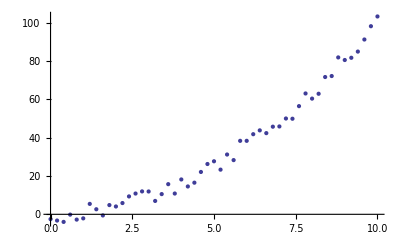

```mathematica
xydata = Table[{n,n^2+5*RandomReal[{-1,1}]}, {n,0,10,0.2}]
ListPlot[xydata]
```

(b) In the cell below, Export the xydata array to a file in your working directory named "xydata.txt" using the "Table" format specifier.  Note that if we were to use a filename with a ".dat" extension, "Table" would be the default format and would not need to be specified.  In this example, because we are using a ".txt" file extension, we need to specify the output format explicitly.  The "Table" format uses tabs to delimit (i.e. separate) the columns in the output file, though options are available for using other delimiters (e.g. commas or spaces).

In a separate cell, Import the data from "xydata.txt" using a "Table" format specifier to tell Mathematica what kind of data to prepare for.  The imported list should look identical to the original xydata.

Also open the "xydata.txt" file using external software -- try both a text editor (e.g. Notepad, Wordpad, or TextEdit) and a spreadsheed (e.g. Microsoft Excel).  Why do so many digits appear after the decimal point?

```mathematica
Export["xydata.txt",xydata,"Table"]
```

xydata.txt

```mathematica
Import["xydata.txt","Table"]
```

{{0.,-1.3518},{0.2,3.0912},{0.4,-2.39005},{0.6,3.89235},{0.8,0.940649},{1.,-1.812},{1.2,4.221},{1.4,5.76574},{1.6,3.86763},{1.8,8.12398},{2.,2.10735},{2.2,3.71631},{2.4,5.83583},{2.6,6.59629},{2.8,3.51087},{3.,13.1119},{3.2,12.9728},{3.4,8.47537},{3.6,12.869},{3.8,16.9988},{4.,17.3617},{4.2,18.5026},{4.4,20.9406},{4.6,23.4147},{4.8,27.3533},{5.,24.2326},{5.2,30.0744},{5.4,24.3726},{5.6,31.9053},{5.8,32.779},{6.,36.19},{6.2,34.3911},{6.4,36.6991},{6.6,42.9695},{6.8,42.9901},{7.,53.5219},{7.2,56.1532},{7.4,55.0447},{7.6,59.3346},{7.8,60.805},{8.,62.3465},{8.2,65.89},{8.4,69.3981},{8.6,73.9251},{8.8,82.081},{9.,84.4402},{9.2,84.1731},{9.4,92.9408},{9.6,92.1717},{9.8,95.1055},{10.,96.4332}}

(c) If you want your data file to be nicely formatted, you will be dissapointed to find that Mathematica doesn't make this easy.  But it can be done.  Evaluate this example, which involves converting numerical data into nicely formatted strings prior to export.  Open the resulting file in an external text editor to verify the results.

```mathematica
niceoutput = Map[ToString[NumberForm[#,{10,6},NumberPadding->{" ","0"}]]&,xydata,{2}]
Export["xydata.txt",niceoutput,"Table"]
```

{{    0.000000,   -1.351800},{    0.200000,    3.091204},{    0.400000,   -2.390051},{    0.600000,    3.892346},{    0.800000,    0.940649},{    1.000000,   -1.812004},{    1.200000,    4.220997},{    1.400000,    5.765743},{    1.600000,    3.867632},{    1.800000,    8.123985},{    2.000000,    2.107354},{    2.200000,    3.716309},{    2.400000,    5.835825},{    2.600000,    6.596287},{    2.800000,    3.510874},{    3.000000,   13.111863},{    3.200000,   12.972799},{    3.400000,    8.475369},{    3.600000,   12.869019},{    3.800000,   16.998774},{    4.000000,   17.361714},{    4.200000,   18.502604},{    4.400000,   20.940622},{    4.600000,   23.414725},{    4.800000,   27.353322},{    5.000000,   24.232640},{    5.200000,   30.074404},{    5.400000,   24.372633},{    5.600000,   31.905279},{    5.800000,   32.779030},{    6.000000,   36.190033},{    6.200000,   34.391147},{    6.400000,   36.699136},{    6.600000,   42.969510},{    6.800000,   42.990094},{    7.000000,   53.521896},{    7.200000,   56.153165},{    7.400000,   55.044708},{    7.600000,   59.334625},{    7.800000,   60.805004},{    8.000000,   62.346497},{    8.200000,   65.889988},{    8.400000,   69.398052},{    8.600000,   73.925144},{    8.800000,   82.080962},{    9.000000,   84.440233},{    9.200000,   84.173127},{    9.400000,   92.940801},{    9.600000,   92.171659},{    9.800000,   95.105541},{   10.000000,   96.433247}}

xydata.txt

(d) There are times when you need more control over the input/output process, particularly when dealing with non-standard formats that involve a combination of data types.  We include one example here of a low-level routine for reading selected portions of a standard data file.

```mathematica
instream = OpenRead["xydata.txt"];  (* open the file as an input stream *)
ReadList[instream,{Number,Number},5]  (* read 5 xy data pairs *)
Skip[instream, String, 15]  (* skip 15 rows *)
ReadList[instream,{Number,Number},5]  (* read 5 xy data pairs *)
Close[instream]; (* close the file *)
```

{{0.,-1.3518},{0.2,3.0912},{0.4,-2.39005},{0.6,3.89235},{0.8,0.940649}}

{{4.,17.3617},{4.2,18.5026},{4.4,20.9406},{4.6,23.4147},{4.8,27.3533}}

(e) In the cell below, generate some three-column numerical data (i.e. a list of three-element lists) and export it to a data file in "Table" format.  Show the result to your TA.

```mathematica
mydata = Table[{n,2*n,3*n},{n,0,10,.1}];
mynicedata = Map[ToString[NumberForm[#,{10,6},NumberPadding->{" ","0"}]]&,mydata,{2}];
Export["mydata.txt",mynicedata,"Table"];
```

### (#6) X-ray scattering data (20 min)

We learned in a previous lab exercise that the wavevector (k) of a light wave propagating through a real material typically has both real and imaginary components, causing the wave to behave like an exponentially-decaying sinusoid of the form ⅇ^-k_ix cos(k_r x).  The imaginary component of the wavevector (k_i) is responsible for the decay term, which causes most of the light to be absorbed after penetrating a short distance into the material.  This penetration depth (also called absorption length) is computed as s=1/k_i.

(a) In addition to importing local data files, it is possible to import ascii data files available on the internet.  Evaluate the cell below to download some numerical data from Lawrence-Berkeley National Laboratory.  This data measures the x-ray scattering factor (f) of solid copper metal as a function of x-ray energy (E, first column).  Because f is proportional to the complex wavevector, it also has both real (f_r, 2nd column) and imaginary (f_i, 3rd column) parts.  Observe that the column titles have been included with the data.  Also notice that because f_r could not be reliably measured below 29 eV, it was recorded as -9999.  Delete the lengthy output before proceeding to the next part so that it won't be in the way.

```mathematica
scatteringdata =Import["http://henke.lbl.gov/optical_constants/sf/cu.nff","Table"];
```

(b) In the cell below, Drop the column titles from your list of data and Select the data points for which f_r>0 (use #[[2]] to refer to the second column).  Then Transpose the data and name the result {energy, freal, fimag}, effectively splitting the data into three component lists.  When you are sure that you have succeded, suppress the output with a semicolon.

```mathematica
noTitle = Rest[scatteringdata];
positive = Select[noTitle,#[[2]]>0&];
{energy,freal,fimag} = Transpose[positive];
```

(c) The wavevector (k) is related to the complex scattering factor (f) according to the equation k=2ρ r_0 λ f, where ρ is the atomic density of the material, r_0 is the classical electron radius, and λ is the vacuum wavelength of the light.  In the cell below, use this formula on your list of scattering factors to obtain a list of wavevectors.  Because you have the real and imaginary parts of the scattering factor stored separately, it will be convenient to compute the real and imaginary parts of k separately.  Thus, you are going to create two separate lists (name them kreal and kimag) rather than one.

Hints: We have already provided the physical constants required, though you will need to compute the wavelength yourself.  From basic quantum physics, we know that wavelength (λ) depends on energy (E) according to λ=h c/E, where h is Planck's constant and c is the vacuum speed of light.  This means that we need a list of wavelengths, one for each energy.  Because mathematical functions tend to be Listable, you should be able to multipy and divide these lists (e.g. energy, wavelength, freal, kimag, etc.) just like ordinary variables.

```mathematica
rho = 4/3.61^3; (* density of copper in atoms per cubic Angstrom *)
hc = 12398.5; (* Planck's constant × speed of light in eV×Angstroms *)
radius = 2.82*^-5; (* classical electron radius in Angstroms *) 
λ = hc/energy;
kreal = 2 rho radius λ freal;
kimag = 2 rho radius λ fimag;
```

(d) Use your list of k_i values to compute a list of penetration depths (s = 1/k_i), and multiply by a practical factor of 10^-4 so that result will be expressed in microns rather than Angstroms.  Then Transpose the resulting list with the energy list, so that you get a list of {E, s} data points, and name the output penetration.

```mathematica
penetration = (1/kimag)*10*^-4;
```

(e) Use your list of k_r values to compute a list of index-of-refraction values (n=1-(λ k_r)/(4π)).  Then Transpose the resulting list with the energy list, so that you get a list of {E, n} data points, and name the output refraction.

```mathematica
n = (1-(λ kreal)/(4π));
refraction =Transpose[ {energy,n}];
```

(f) Evaluate the cell below to plot the x-ray penetration depth and the index of refraction of copper metal as a function of energy.  We use ListLogLogPlot for the penetration depth and ListLogLinearPlot for the index of refraction.  In the penetration-depth plot, you should notice two sharp "cliffs" correpsonding to the K (near 9 keV) and L (near 1 keV) aborption edges.  Each absorption edge indicates an x-ray energy large enough to knock electrons out a specific atomic core shell (the K shell is the deepest shell).  This greater propensity to interact with an electron above the edge increases the absorption and decreases the penetration depth.  You may be concerned that your n values violate the special theory of relativity -- the Wikipedia article on Refractive Index addresses this issue and uses x-ray scattering as an example.

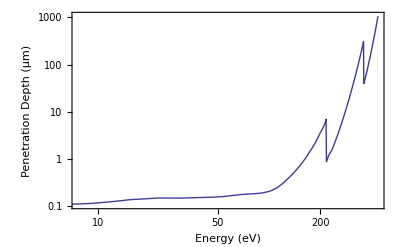

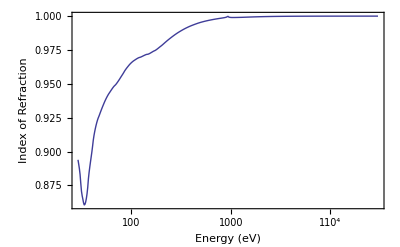

```mathematica
ListLogLogPlot[ penetration,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Penetration Depth (μm)"}]
ListLogLinearPlot[refraction,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Energy (eV)","Index of Refraction"}]
```

### (#7) Import/Export/Processing of ascii-character data (20 min)

(a) Download the "funwithstring.txt" file from the course website into your working directory, and Import it into a list called firsttry, assuming a "Table" format.  Examine firsttry carefully using both TableForm and InputForm.  Also measure the length of each of its rows (i.e. Length/@firsttry).  You should see that this list has some problems -- explain them to your TA.

```mathematica
SetDirectory[NotebookDirectory[]]
firsttry = Import["funwithstring.txt","Table"]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

{{Maines,,Myra,,911,Louden,Street,,Dover,,UT,,84607},{Downe,,Doug,,8988,Romero,Court,,Lucin,,UT,,84604},{Stein,,Frank,N.,,1602,Shelley,Pass,,Altus,,UT,,84609},{Angels,,C.,N.,,30,Stevenson,Road,,Topaz,,UT,,84600},{D'lyve,,Barry,,6626,Edgar,Avenue,,Notom,,UT,,84603},{Moore-Tishan,,Anita,,300,Irving,Hollow,,Arago,,UT,,84608},{Goein,,Imus,B.,,667,Ellison,Plaza,,Heist,,UT,,84605},{Bach,,Al,B.,,16022,Stoker,Blvd,,Paria,,UT,,84601},{Heresoon,,Yule,B.,,13807,Leroux,Lane,,Giles,,UT,,84606},{Balmde,,Ben,N.,,126,Hitchcock,Way,,Ophir,,UT,,84602}}

(b) Take a few minutes to browse through the tutorial on Reading Textual Data, which demonstrates the capabilities of the ReadList function.  Then use ReadList to import "funwithstring.txt" into a list called secondtry.  Specify the String object type, so that each row of data gets imported as one long string -- this should produce a list of 10 strings.

```mathematica
secondTry=ReadList["funwithstring.txt","String"]
Dimensions[secondTry]
```

{Maines, Myra, 911 Louden Street, Dover, UT, 84607,Downe, Doug, 8988 Romero Court, Lucin, UT, 84604,Stein, Frank N., 1602 Shelley Pass, Altus, UT, 84609,Angels, C. N., 30 Stevenson Road, Topaz, UT, 84600,D'lyve, Barry, 6626 Edgar Avenue, Notom, UT, 84603,Moore-Tishan, Anita, 300 Irving Hollow, Arago, UT, 84608,Goein, Imus B., 667 Ellison Plaza, Heist, UT, 84605,Bach, Al B., 16022 Stoker Blvd, Paria, UT, 84601,Heresoon, Yule B., 13807 Leroux Lane, Giles, UT, 84606,Balmde, Ben N., 126 Hitchcock Way, Ophir, UT, 84602}

{10}

(c) Map StringSplit onto each of the long strings within secondtry in order to break them up into shorter strings based on the locations of any commas present.  Hints: This will require you to specify "," (including the quotes) as the delimiter in the 2nd argument of StringSplit.  Name the result nicetry and verify that it has Dimensions of {10,6}.

```mathematica
niceTry = StringSplit[secondTry,","]
Dimensions[niceTry]
```

{{Maines, Myra, 911 Louden Street, Dover, UT, 84607},{Downe, Doug, 8988 Romero Court, Lucin, UT, 84604},{Stein, Frank N., 1602 Shelley Pass, Altus, UT, 84609},{Angels, C. N., 30 Stevenson Road, Topaz, UT, 84600},{D'lyve, Barry, 6626 Edgar Avenue, Notom, UT, 84603},{Moore-Tishan, Anita, 300 Irving Hollow, Arago, UT, 84608},{Goein, Imus B., 667 Ellison Plaza, Heist, UT, 84605},{Bach, Al B., 16022 Stoker Blvd, Paria, UT, 84601},{Heresoon, Yule B., 13807 Leroux Lane, Giles, UT, 84606},{Balmde, Ben N., 126 Hitchcock Way, Ophir, UT, 84602}}

{10,6}

(d) Reverse the order of the given names and surnames (so as to show given name first) in nicetry, and sort the individuals in the list by zip code, displaying the final result in TableForm.

Hints: (1) Use a single line of code to Transpose nicetry into six component lists: {surname, givenname, streetaddress, city, state, zip}, where the zip-code strings get promptly converted to integers.  (2) Reconstruct the name-address list as the Transpose of {givenname, surname, streetaddress, city, state, ToExpression[zip]} and name the result nexttry.  (3) Then Sort nextry by zip code (i.e. #[[6]]).

```mathematica
{surname,givenName,streetAddress, city, state, zip} = Transpose[niceTry];
nextTry = Transpose[{givenName,surname,streetAddress,city,state,ToExpression[zip]}]
Sort[nextTry,#1[[6]]<#2[[6]]&]
```

{{ Myra,Maines, 911 Louden Street, Dover, UT,84607},{ Doug,Downe, 8988 Romero Court, Lucin, UT,84604},{ Frank N.,Stein, 1602 Shelley Pass, Altus, UT,84609},{ C. N.,Angels, 30 Stevenson Road, Topaz, UT,84600},{ Barry,D'lyve, 6626 Edgar Avenue, Notom, UT,84603},{ Anita,Moore-Tishan, 300 Irving Hollow, Arago, UT,84608},{ Imus B.,Goein, 667 Ellison Plaza, Heist, UT,84605},{ Al B.,Bach, 16022 Stoker Blvd, Paria, UT,84601},{ Yule B.,Heresoon, 13807 Leroux Lane, Giles, UT,84606},{ Ben N.,Balmde, 126 Hitchcock Way, Ophir, UT,84602}}

{{ C. N.,Angels, 30 Stevenson Road, Topaz, UT,84600},{ Al B.,Bach, 16022 Stoker Blvd, Paria, UT,84601},{ Ben N.,Balmde, 126 Hitchcock Way, Ophir, UT,84602},{ Barry,D'lyve, 6626 Edgar Avenue, Notom, UT,84603},{ Doug,Downe, 8988 Romero Court, Lucin, UT,84604},{ Imus B.,Goein, 667 Ellison Plaza, Heist, UT,84605},{ Yule B.,Heresoon, 13807 Leroux Lane, Giles, UT,84606},{ Myra,Maines, 911 Louden Street, Dover, UT,84607},{ Anita,Moore-Tishan, 300 Irving Hollow, Arago, UT,84608},{ Frank N.,Stein, 1602 Shelley Pass, Altus, UT,84609}}

### (#8) Exporting XML Data (10 min)

A common format for transmitting data between different systems or programs is called Externsible Mark-up Language (XML).  It is particularly widely used for sharing data over the internet.  If you are familiar with HTML, it has a similar structure.  There are a lot of details to the protocol but the basic elements we’ll worry about are the XML declaration, XML elements, XML attributes, and XML values.

The first line in an XML file is the XML declaration which flags the file as XML and gives the XML version number.  It looks like the following:
<?xml version=”1.0”?>

The rest of the file consists of XML elements.  These consist of an opening tag, optional atributes, data (or values), and a closing tag.  Here is an example.

<temperature unit=”Kelvin”>
301
</temperature>

The opening tag has an opening angle bracket and ends wtih a closing angle bracket.  The bracket is followed b y the name of the tag.  In this case the tag is temperature.

The optional attribute(s) have a format name=”value”.  The value must be in quotes.  They are contained inside the opening tag.

The opening tag is followed by the value of the tag.  The value can have other tags nested inside it.

The final part of the XML element is the closing tag.  It starts with an angle bracket following by a / character and then the name of the opening tag.  Evering opening XML tag must have a corresponding closing tag.

The “extensible” part of XML lies in the fact that there are no predefined restrictions on that names of the XML tags or their contents.  This makes it a very general format that can be used for a lot of purposes.  For example, Wolfram has defined a partricular set of tags that can be used to describe Mathematica expressions.  You can export your data in XML format and read it back into Mathematica with relative ease.  Execute the following sequence of statements to see how this is done.  Explain the output to your TA.

```mathematica
SetDirectory[NotebookDirectory[]]
xData=Range[5];
Export["data.xml",xData]
FilePrint["data.xml"]
(* clear the data and read it back in *)
Clear[xData]
Import["data.xml"]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

data.xml

<?xml version='1.0'?>
<!DOCTYPE Expression SYSTEM 'http://www.wolfram.com/XML/notebookml1.dtd'>
<Expression xmlns:mathematica='http://www.wolfram.com/XML/'
    xmlns='http://www.wolfram.com/XML/'>
 <Function>
  <Symbol>List</Symbol>
  <Number>1</Number>
  <Number>2</Number>
  <Number>3</Number>
  <Number>4</Number>
  <Number>5</Number>
 </Function>
</Expression>

{1,2,3,4,5}

The <!DOCTYPE> tag in the Mathematica output tells XML readers what format to expect in the data.  Likewise, the extra data in the root Expression tag describe the format use for the following data.

### (#9) Importing XML Data (10 min)

Importing XML data produced by programs other than Mathematica is more involveved than importing data created by Mathematica.  You’ll need to either have documentation on the format used or figure it out by examining the contents of the file.

Here is an example of what some temperature data might look like.

```mathematica
SetDirectory[NotebookDirectory[]];
FilePrint["temp.xml"]
```

<?xml version='1.0'?>
<measurement>
 <temperature>
  <degrees>
   321
  </degrees>
  <units>
   Kelvin
  </units>
 </temperature>
 <temperature>
  <degrees>
   307
  </degrees>
  <units>
   Kelvin
  </units>
 </temperature>
 <temperature>
  <degrees>
   312
  </degrees>
  <units>
   Kelvin
  </units>
 </temperature>
 <temperature>
  <degrees>
   319
  </degrees>
  <units>
   Kelvin
  </units>
 </temperature>
 <temperature>
  <degrees>
   303
  </degrees>
  <units>
   Kelvin
  </units>
 </temperature>
 <temperature>
  <degrees>
   290
  </degrees>
  <units>
   Kelvin
  </units>
 </temperature>
</measurement>

It has a root tag of measurement followed by an embedded sequence of temperature tags.  Each temperature tag has two embedded tags, one for the number of degrees and one for the units.  Reading this file using only the tools you have acquired so far takes a little work to wend through the embedded structures.  Here is an example of one way to do it.  These two functions produce a list of the temperature data in the file.  In the interest of simplicity and clarity, the routines don’t do any internal checking on the structure of the data.

```mathematica
parseXML[file_]:=Module[{xml,dv},
(* /assume top levels is an XMLObject of type "Document" *)
xml=Import[file];
(* Check list of elements *)
xml=xml[[2]];
getTemperature/@xml[[3]]
]
getTemperature[elemt_]:=Module[{subel},
subel=elemt[[3]];
lst=Select[subel,#[[1]]== "degrees"&];
lst[[1,3]]//First
]
parseXML["temp.xml"]
```

{321,307,312,319,303,290}

Explain how these routines work to your TA.

Here is a simpler way of extracting the data using pattern matching.

```mathematica
patternXML[file_]:=Module[{xml},
xml=Import[file];
Cases[xml, XMLElement["degrees",_,{temp_}]:>ToExpression[temp], Infinity]
]
patternXML["temp.xml"]
```

{321,307,312,319,303,290}

The trick in the simplification is the use of the Cases statement which relies on pattern matching to find just those XML elements which contain the data we are intereested in.  the _ in the pattern means to match any list of  attributes (or non attributes).  The temp_ replacement rule replaces each XML pattern that matches the given pattern with the temperature found in that pattern.

The delayed replacement rule :>  (typeed :>) is necessary to enable temp to be assigned before the call to ToExpression which converts the temperature from a String to a Real.

## Multimedia (25 min)

Multimedia (images, audio and video) tools have become an invaluable means of recording, storing, sharing and analyzing scienfic data.  Mathematica currenty supports a large number of Import/Export formats.  The Import and Export reference pages are fairly limited, but contain links to a number of good tutorials.  Also see the complete list of supported formats, grouped by media type or grouped alphabetically, to learn about the special options available to individual formats.  If you use a common extention (e.g.  ".jpg"), Mathematica will automatically figure out which format you want.  Otherwise, you can provide a format specifier (e.g. "JPEG") as an argument to Import or Export.

### (#10) Audio (15 min)

(a) The DC guide page on Sound and Sonification contains links to most of the standard functions for creating and analyzing audio signals.  Spend 10 minutes working through the "Basic Examples" on each of these reference pages.  If you have have a strong interest in music and/or audio, you may also want to explore the special Music and Audio packages.

(b) Evaluate the cell below to see some instrumental-audio clips available via ExampleData.  One can also conveniently Import audio data from disk or from the internet.  Use earphones to listen to the clip that we loaded here (the TAs should have headphones available if you don't have your own).  Study the output from ReplacePart to see how Mathematica organizes sound data.  Observe that the only metadata stored is the sample frequency.  Sound, like Graphics, is a wrapper that delivers its content in a user-friendly format (i.e. a cute graphical-interface box).

```mathematica
ExampleData["Sound"]
horn = ExampleData[{"Sound","FrenchHorn"}]
ReplacePart[horn,{1,1}->"datagoeshere"]//InputForm
```

{{Sound,AltoFlute},{Sound,AltoFluteScale},{Sound,AltoSaxophone},{Sound,AltoSaxophoneScale},{Sound,Apollo11PhoneCall},{Sound,Apollo11ReturnSafely},{Sound,Apollo11SmallStep},{Sound,Apollo13Countdown},{Sound,Apollo13Problem},{Sound,BalloonPop},{Sound,BassClarinet},{Sound,BassClarinetScale},{Sound,BassFlute},{Sound,BassFluteScale},{Sound,Bassoon},{Sound,BassoonScale},{Sound,BassTrombone},{Sound,BassTromboneScale},{Sound,Burst100},{Sound,Burst1000},{Sound,Burst7350},{Sound,Cello},{Sound,CelloPizzicato},{Sound,CelloPizzicatoScale},{Sound,CelloScale},{Sound,Clarinet},{Sound,ClarinetScale},{Sound,CrashCymbal},{Sound,DoubleBass},{Sound,DoubleBassPizzicato},{Sound,DoubleBassPizzicatoScale},{Sound,DoubleBassScale},{Sound,Flute},{Sound,FluteScale},{Sound,FrenchHorn},{Sound,FrenchHornScale},{Sound,LinearSweep},{Sound,NoiseBlue},{Sound,NoiseBrown},{Sound,NoisePink},{Sound,NoiseViolet},{Sound,NoiseWhite},{Sound,Oboe},{Sound,OboeScale},{Sound,Piano},{Sound,PianoScale},{Sound,SopranoSaxophone},{Sound,SopranoSaxophoneScale},{Sound,Square10},{Sound,Square100},{Sound,Square1000},{Sound,Square7350},{Sound,TenorTrombone},{Sound,TenorTromboneScale},{Sound,TestIntermodulationDistortion},{Sound,Trumpet},{Sound,TrumpetScale},{Sound,Tuba},{Sound,TubaScale},{Sound,Viola},{Sound,ViolaScale},{Sound,Violin},{Sound,ViolinScale}}

-Graphics-

Sound[SampledSoundList["datagoeshere", 22050]]

(c) Make a modified version of this horn sound that plays the same note an octave lower.  You might use ReplacePart on horn to cut the sample rate in half (i.e. from 22050 Hz to 11025 Hz).  Or you could extract the audio data within horn, and manually invoke SampledSoundList with the lower frequency, followed by Sound or EmitSound.  Either way, name the new sound lowhorn.  Why does lowhorn play twice as long as horn?

```mathematica
hornData = horn[[1,1]];
lowHorn = Sound[SampledSoundList[hornData,11025]]
```

-Graphics-

(d) Export lowhorn to a ".wav" file in your working directory and play it with external software.

```mathematica
Export["lowhorn.wav",lowHorn]
```

lowhorn.wav

### (#11) Video (10 min)

Mathematica can import and export a nubmer of video formats.  For our purposes, we’ll focus on the single tasks of exporting animations which you might want to embed in a presentation or display on the web.

The simplest (and usually most inadequate) way to export data is to export an animation directly.  You can export AVI, MOV, or SWF formats.  AVI files are the largest but most universally accepted by programs such as PowerPoint.  MOVE format files are much smaller and faster if your target software supports them.  SWF files are also much smaller and work well on web pages.

Execute the following commands to create an animation and store it as an AVI file.  Then view the file using Windows Media player on your desktop by double clicking on it.

```mathematica
SetDirectory[NotebookDirectory[]]
Animate[Plot[Sin[2 Pi (x-t)],{x,0,2}],{t,0,2}];
Export["sine.avi",%]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

sine.avi

A better way to create graphics (usually smoother, smaller, and without non-functional controls) is to create an array of graphics objects and then export that.

```mathematica
gArray=Table[Plot[Sin[2 Pi(x-t)],{x,0,2}],{t,0,2,0.05}];
Export["sine2.avi",gArray, AnimationRate->10]
```

sine2.avi

Create an animation file of the function f(x,y,t)=3 cos(0.2 t) exp(-1/3 (x^2+y^2)) for x and y from -5 to 5 and t from 0 to 20π.  Embed your file in a PowerPoint presentation and who it to your TA.  Use PlotRange->{All, All, {-3,3}} in order to preserve the scale on your plots.

```mathematica
myFuncArray= Table[Plot3D[3Cos[0.2t]Exp[-1/3(x^2+y^2)],{x,-5,5},{y,-5,5},PlotRange->{All,All,{-3,3}}],{t,0,20π,1}];
Export["myVideo.avi",myFuncArray,AnimationRate->10]
```

myVideo.avi

## Integrated Data Sources (10 min)

Briefly review the DC guide page on Mathematica's Integrated Data Sources, a diverse collection of internet-accessible data sources, some of which are continually updated.  Whenever you query one of the data sources, the requested data is automatically downloaded to your computer and imported into your notebook for analysis and/or display.  While we only have time to explore a few of the available data sources in this section, you are encourage to explore the others later on your own.  You may also be interested in the Units package and the Physical Constants package.

### (#12) Element Data (10 min)

(a) ElementData provides a variety of information on each element in the periodic table.  Evaluate the cell below, where we display (1) a list of the elements in the database, (2) a list of the properties stored for each element, (3) the atomic number of iron, and (4) a list of the property values stored for iron.  Carefully study how ElementData is used to obtain each of these three lists, and explain your observations to your TA.  Before you proceed to the next part, delete the lengthy output so that it won't be in the way.

```mathematica
ElementData[];
properties = ElementData["Properties"];
ElementData["Iron","AtomicNumber"]
MatrixForm/@{#,ElementData["Iron",#]}& /@ properties // TableForm;
```

26

(b)  Of course, it isn't possible to include every property for every element in the periodic table.  And you probably saw that some of the properties of iron were listed as Missing because they were either "NotAvailable", "NotApplicable", or "Unknown".  Evaluate the cell below to create a function called skipmissing that eliminates any Missing items from a list of data.  We test it for one simple example.  Before you proceed to the next part, delete the lengthy output so that it won't be in the way.

```mathematica
skipmissing[data_] := Select[data,!MemberQ[Flatten[#],_Missing]&]

{#,ElementData[#,"MagneticType"],ElementData[#,"ElectricalType"]}&/@ ElementData[]
% // skipmissing
```

{{Lithium,Paramagnetic,Conductor},{Beryllium,Diamagnetic,Conductor},{Boron,Diamagnetic,Insulator},{Carbon,Diamagnetic,Conductor},{Sodium,Paramagnetic,Conductor},{Magnesium,Paramagnetic,Conductor},{Aluminum,Paramagnetic,Conductor},{Silicon,Diamagnetic,Semiconductor},{Phosphorus,Diamagnetic,Conductor},{Sulfur,Diamagnetic,Insulator},{Chlorine,Diamagnetic,Insulator},{Potassium,Paramagnetic,Conductor},{Calcium,Paramagnetic,Conductor},{Scandium,Paramagnetic,Conductor},{Titanium,Paramagnetic,Conductor},{Vanadium,Paramagnetic,Conductor},{Chromium,Antiferromagnetic,Conductor},{Manganese,Paramagnetic,Conductor},{Iron,Ferromagnetic,Conductor},{Cobalt,Ferromagnetic,Conductor},{Nickel,Ferromagnetic,Conductor},{Copper,Diamagnetic,Conductor},{Zinc,Diamagnetic,Conductor},{Gallium,Diamagnetic,Conductor},{Germanium,Diamagnetic,Semiconductor},{Arsenic,Diamagnetic,Conductor},{Bromine,Diamagnetic,Insulator},{Rubidium,Paramagnetic,Conductor},{Strontium,Paramagnetic,Conductor},{Yttrium,Paramagnetic,Conductor},{Zirconium,Paramagnetic,Conductor},{Niobium,Paramagnetic,Conductor},{Molybdenum,Paramagnetic,Conductor},{Technetium,Paramagnetic,Conductor},{Ruthenium,Paramagnetic,Conductor},{Rhodium,Paramagnetic,Conductor},{Palladium,Paramagnetic,Conductor},{Silver,Diamagnetic,Conductor},{Cadmium,Diamagnetic,Conductor},{Indium,Diamagnetic,Conductor},{Tin,Diamagnetic,Conductor},{Antimony,Diamagnetic,Conductor},{Tellurium,Diamagnetic,Semiconductor},{Iodine,Diamagnetic,Insulator},{Cesium,Paramagnetic,Conductor},{Barium,Paramagnetic,Conductor},{Lanthanum,Paramagnetic,Conductor},{Cerium,Paramagnetic,Conductor},{Praseodymium,Paramagnetic,Conductor},{Neodymium,Paramagnetic,Conductor},{Samarium,Paramagnetic,Conductor},{Europium,Paramagnetic,Conductor},{Gadolinium,Ferromagnetic,Conductor},{Terbium,Paramagnetic,Conductor},{Dysprosium,Paramagnetic,Conductor},{Holmium,Paramagnetic,Conductor},{Erbium,Paramagnetic,Conductor},{Thulium,Paramagnetic,Conductor},{Ytterbium,Paramagnetic,Conductor},{Lutetium,Paramagnetic,Conductor},{Hafnium,Paramagnetic,Conductor},{Tantalum,Paramagnetic,Conductor},{Tungsten,Paramagnetic,Conductor},{Rhenium,Paramagnetic,Conductor},{Osmium,Paramagnetic,Conductor},{Iridium,Paramagnetic,Conductor},{Platinum,Paramagnetic,Conductor},{Gold,Diamagnetic,Conductor},{Mercury,Diamagnetic,Conductor},{Thallium,Diamagnetic,Conductor},{Lead,Diamagnetic,Conductor},{Bismuth,Diamagnetic,Conductor},{Thorium,Paramagnetic,Conductor},{Protactinium,Paramagnetic,Conductor},{Uranium,Paramagnetic,Conductor},{Plutonium,Paramagnetic,Conductor}}

(c) In this cell, create a 2D list that contains a pair of Kelvin-degree temperatures, the "AbsoluteMeltingPoint" and the "AbsoluteBoilingPoint", for each element in the database.  Then use skipmissing to eliminate the pairs that are Missing one or both of these temperatures, and employ N to ensure that all of the entries contain true floating-point data.

```mathematica
skipmissing[data_] := Select[data,!MemberQ[Flatten[#],_Missing]&]

{#,ElementData[#,"AbsoluteMeltingPoint"],ElementData[#,"AbsoluteBoilingPoint"]}&/@ ElementData[]
tempData = % // skipmissing
```

{{Hydrogen,14.01,20.28},{Lithium,453.69,1615.},{Beryllium,1560.,2743.},{Boron,2348.,4273.},{Carbon,3823.,4300.},{Nitrogen,63.05,77.36},{Oxygen,54.8,90.2},{Fluorine,53.5,85.03},{Neon,24.56,27.07},{Sodium,370.87,1156.},{Magnesium,923.,1363.},{Aluminum,933.47,2792.},{Silicon,1687.,3173.},{Phosphorus,317.3,553.6},{Sulfur,388.36,717.87},{Chlorine,171.6,239.11},{Argon,83.8,87.3},{Potassium,336.53,1032.},{Calcium,1115.,1757.},{Scandium,1814.,3103.},{Titanium,1941.,3560.},{Vanadium,2183.,3680.},{Chromium,2180.,2944.},{Manganese,1519.,2334.},{Iron,1811.,3134.},{Cobalt,1768.,3200.},{Nickel,1728.,3186.},{Copper,1357.77,3200.},{Zinc,692.68,1180.},{Gallium,302.91,2477.},{Germanium,1211.4,3093.},{Arsenic,1090.,887.},{Selenium,494.,958.},{Bromine,265.8,332.},{Krypton,115.79,119.93},{Rubidium,312.46,961.},{Strontium,1050.,1655.},{Yttrium,1799.,3618.},{Zirconium,2128.,4682.},{Niobium,2750.,5017.},{Molybdenum,2896.,4912.},{Technetium,2430.,4538.},{Ruthenium,2607.,4423.},{Rhodium,2237.,3968.},{Palladium,1828.05,3236.},{Silver,1234.93,2435.},{Cadmium,594.22,1040.},{Indium,429.75,2345.},{Tin,505.08,2875.},{Antimony,903.78,1860.},{Tellurium,722.66,1261.},{Iodine,386.85,457.4},{Xenon,161.3,165.1},{Cesium,301.59,944.},{Barium,1000.,2143.},{Lanthanum,1193.,3737.},{Cerium,1071.,3633.},{Praseodymium,1204.,3563.},{Neodymium,1294.,3373.},{Promethium,1373.,3273.},{Samarium,1345.,2076.},{Europium,1095.,1800.},{Gadolinium,1586.,3523.},{Terbium,1629.,3503.},{Dysprosium,1685.,2840.},{Holmium,1747.,2973.},{Erbium,1770.,3141.},{Thulium,1818.,2223.},{Ytterbium,1092.,1469.},{Lutetium,1936.,3675.},{Hafnium,2506.,4876.},{Tantalum,3290.,5731.},{Tungsten,3695.,5828.},{Rhenium,3459.,5869.},{Osmium,3306.,5285.},{Iridium,2739.,4701.},{Platinum,2041.4,4098.},{Gold,1337.33,3129.},{Mercury,234.32,629.88},{Thallium,577.,1746.},{Lead,600.61,2022.},{Bismuth,544.4,1837.},{Polonium,527.,1235.},{Radon,202.,211.3},{Radium,973.,2010.},{Actinium,1323.,3473.},{Thorium,2023.,5093.},{Protactinium,1845.,4273.},{Uranium,1408.,4200.},{Neptunium,917.,4273.},{Plutonium,913.,3503.},{Americium,1449.,2284.},{Curium,1618.,3383.}}

(d) Fit a straight line with zero intercept through the data obtained in the previous cell.  Plot the data and the resulting fit on the same graph with the following options:  {PlotRange → All, Frame → True, FrameLabel → {"Melting Point (K)", "Boiling Point (K)"}}.  What do you learn from this plot?

```mathematica
plotData = Transpose[Rest[Transpose[tempData]]]
FindFit[plotData,A*x,A,x]
```

{{14.01,20.28},{453.69,1615.},{1560.,2743.},{2348.,4273.},{3823.,4300.},{63.05,77.36},{54.8,90.2},{53.5,85.03},{24.56,27.07},{370.87,1156.},{923.,1363.},{933.47,2792.},{1687.,3173.},{317.3,553.6},{388.36,717.87},{171.6,239.11},{83.8,87.3},{336.53,1032.},{1115.,1757.},{1814.,3103.},{1941.,3560.},{2183.,3680.},{2180.,2944.},{1519.,2334.},{1811.,3134.},{1768.,3200.},{1728.,3186.},{1357.77,3200.},{692.68,1180.},{302.91,2477.},{1211.4,3093.},{1090.,887.},{494.,958.},{265.8,332.},{115.79,119.93},{312.46,961.},{1050.,1655.},{1799.,3618.},{2128.,4682.},{2750.,5017.},{2896.,4912.},{2430.,4538.},{2607.,4423.},{2237.,3968.},{1828.05,3236.},{1234.93,2435.},{594.22,1040.},{429.75,2345.},{505.08,2875.},{903.78,1860.},{722.66,1261.},{386.85,457.4},{161.3,165.1},{301.59,944.},{1000.,2143.},{1193.,3737.},{1071.,3633.},{1204.,3563.},{1294.,3373.},{1373.,3273.},{1345.,2076.},{1095.,1800.},{1586.,3523.},{1629.,3503.},{1685.,2840.},{1747.,2973.},{1770.,3141.},{1818.,2223.},{1092.,1469.},{1936.,3675.},{2506.,4876.},{3290.,5731.},{3695.,5828.},{3459.,5869.},{3306.,5285.},{2739.,4701.},{2041.4,4098.},{1337.33,3129.},{234.32,629.88},{577.,1746.},{600.61,2022.},{544.4,1837.},{527.,1235.},{202.,211.3},{973.,2010.},{1323.,3473.},{2023.,5093.},{1845.,4273.},{1408.,4200.},{917.,4273.},{913.,3503.},{1449.,2284.},{1618.,3383.}}

{A→1.8}

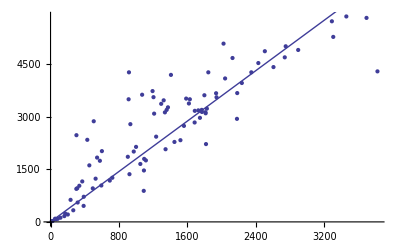

```mathematica
Show[ListPlot[plotData],Plot[1.8x,{x,0,4000}]]
```

## On Your Own (40 min)

### (#13) Reading a CSV data file (10 min)

The file multidata.csv contains data from an experiment recorded in four columns.  The first column is the time in seconds, the second the temperature, the third the magnetic field, and the fourth a voltage on a sensor in millivolts.  Read in the data and create a 3d plot of the calibrated sensor reading as a function of 1/temperature and magnetic field.  The file calibration.csv contains the calibration data for the sensor.  The first column is the sensor reading and the second column is the calibration signal.  (Since your routine should work for a large collection of deata files, you need to do any necessary data manipulation from within Mathematica.  Don’t edit the data files directly.

```mathematica
SetDirectory[NotebookDirectory[]]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

```mathematica
data= Import["multidata.csv","Table"]//TableForm
```

"Data Run UV70954, 5 Sep 2011",,,
time,temp,field,signal
1.398264654,10,0.5,-1.682228097
1.238386895,10,1,-1.799267001
0.918670025,10,1.5,2.262549086
1.492535348,10,2,0.530058055
1.31819091,10,2.5,1.524901411
1.116735376,11,0.5,-0.296661508
0.639363772,11,1,-0.954571168
0.969956053,11,1.5,-1.053507162
1.538761444,11,2,-0.845180493
1.088731598,11,2.5,2.053953755
1.318550959,12,0.5,2.95403241
1.294109246,12,1,0.568640644
0.973536003,12,1.5,2.983087429
0.837045348,12,2,1.380838186
1.281947479,12,2.5,-0.431391963
1.514710418,13,0.5,0.301702645
0.833319877,13,1,2.070526516
1.429926681,13,1.5,0.706694667
0.853489729,13,2,-1.069227726
0.92778341,13,2.5,-0.184224477
1.252153462,14,0.5,-1.96455164
1.001182606,14,1,-2.189493119
1.167908569,14,1.5,-0.963683161
1.157852199,14,2,3.122255047
1.035118011,14,2.5,1.42975053
1.957145803,15,0.5,-1.816856861
1.144342169,15,1,1.357753938
1.401661244,15,1.5,0.854038919
1.982004482,15,2,0.125974676
1.76626603,15,2.5,1.870007278
1.76788224,16,0.5,-2.589498595
1.846001225,16,1,0.95857039
1.440877567,16,1.5,-2.035656639
1.626305355,16,2,1.77711497
1.609337142,16,2.5,3.051002108
2.160905259,17,0.5,-1.879266799
2.102086612,17,1,1.226731263
1.382332016,17,1.5,-0.4511071
1.211976376,17,2,-2.290233726
1.615652073,17,2.5,0.005041227
1.773208017,18,0.5,0.0009201
2.087441562,18,1,0.331506326
1.824112028,18,1.5,-1.925193841
1.311850742,18,2,1.404928074
1.370377103,18,2.5,-1.207437418
1.645067699,19,0.5,-0.028531639
2.164225149,19,1,-0.607119205
1.526644635,19,1.5,0.407459158
1.666822504,19,2,1.909922762
2.374130639,19,2.5,-0.157926033
2.382741674,20,0.5,-1.600534555
2.022029908,20,1,-1.043420098
2.469152899,20,1.5,-2.377145337
2.046749045,20,2,0.864194495
2.484586623,20,2.5,-2.654930909

Create the data.

### (#14) Reading an XML data file (15 min)

The file temperature.xml has temperature readings for an approximate 3 day period in early September 2011 as measured by the BYU weather station.  Plot the temperature at five minute intervals for this time period.  (HINT:  make sure you turn the readings into numbers before trying to plot them.  The AbsoluteTime function may help you with the date and time data.)

### (#15) Saving an animation as five a movie (15 min)

Create a graphical animation of a mass in damped harmonic motion (y=exp(-α t) cos(t ω)).  (No need to draw the spring.) Export it to a file in .avi format that can be embedded in a PowerPoint presentation.  Make sure each frame is drawn using the same scale.